# Elliptical Constraints Figures

I need 2D and 3D figures illustrating the construction

## 2D

{{1,0.5},{1.7,0.1},{0.3,0.9}}

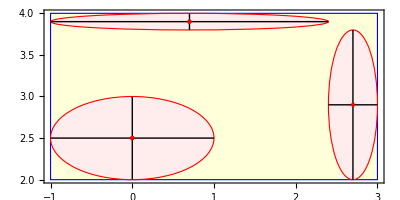

```mathematica
{l,u}={{-1,2},{3,4}};
cs={{0,2.5},{0.7,3.9},{2.7,2.9}};
rs=Table[
Map[Min,{cs⟦i⟧-l,u-cs⟦i⟧}ᵀ],
{i,Length[cs]}]
Graphics[{
{EdgeForm[Blue],LightYellow,Rectangle[l,u]},
Table[{
{EdgeForm[Red],LightPink,Disk[cs⟦i⟧,rs⟦i⟧]},
Line[{cs⟦i⟧-{0,rs⟦i,2⟧},cs⟦i⟧+{0,rs⟦i,2⟧}}],
Line[{cs⟦i⟧-{rs⟦i,1⟧,0},cs⟦i⟧+{rs⟦i,1⟧,0}}],
{Red, Point[cs]}
},{i,Length[cs]}]
},
AspectRatio->Automatic,
Frame->True,
PlotRangePadding->0.2]
```

## 3D

```mathematica
{l,u}={{-1,2,1},{3,4,2}};
cs={{0,2.5,1.3},{0.7,3.9,1.2},{2.7,2.5,1.6}};
rs=Table[
Map[Min,{cs⟦i⟧-l,u-cs⟦i⟧}ᵀ],
{i,Length[cs]}]
Graphics3D[{
{EdgeForm[Blue],Opacity[0.2],LightYellow,Cuboid[l,u]},
Table[{
{EdgeForm[Red],LightPink,Opacity[0.3],Ellipsoid[cs⟦i⟧,rs⟦i⟧]},
{Black, Thick,
(*{Red, PointSize[0.02],Point[cs]},*)
Line[{cs⟦i⟧-{rs⟦i,1⟧,0,0},cs⟦i⟧+{rs⟦i,1⟧,0,0}}],
Line[{cs⟦i⟧-{0,rs⟦i,2⟧,0},cs⟦i⟧+{0,rs⟦i,2⟧,0}}],
Line[{cs⟦i⟧-{0,0,rs⟦i,3⟧},cs⟦i⟧+{0,0,rs⟦i,3⟧}}]
},
{Red, Point[cs]}
},{i,Length[cs]}]
},
BoxRatios->Automatic,
Boxed->True,
Axes->True,
AxesLabel->Table[StringForm["x_(``)",i],{i,3}],
PlotRangePadding->0.2]
```

{{1,0.5,0.3},{1.7,0.1,0.2},{0.3,0.5,0.4}}

-Graphics3D-

```mathematica
?Cuboid
```

```mathematica
c={0,2.5};
r=Map[Min,{c-l,u-c}ᵀ];
BoxBounds=Apply[And,Table[ l⟦i⟧<vars⟦i⟧ <u⟦i⟧,{i,Length[vars]}]];
Show[
RegionPlot[ BoxBounds,{x,-2,4},{y,1,5},
PlotPoints->100,
PlotStyle->LightYellow],
Graphics[{
{EdgeForm[Red],LightPink,Disk[c,r]},
Line[{c-{0,r⟦2⟧},c+{0,r⟦2⟧}}],
Line[{c-{r⟦1⟧,0},c+{r⟦1⟧,0}}],
{Red, Point[c]}
}],
AspectRatio->Automatic
]
```

```mathematica
{l,u}={{-1,2,1},{3,4,6}};
vars={x,y,z};
c={0,2.5,1.2};
r=Map[Min,{c-l,u-c}ᵀ];
BoxBounds=Apply[And,Table[ l⟦i⟧<vars⟦i⟧ <u⟦i⟧,{i,Length[vars]}]];
Show[
RegionPlot3D[ BoxBounds,{x,-2,4},{y,1,5},{z,0, 7},
PlotPoints->100,
PlotStyle->Opacity[0.0]],
Graphics3D[{
{EdgeForm[Red],LightPink,Ellipsoid[c,r]},
Line[{c-{0,r⟦2⟧,0},c+{0,r⟦2⟧,0}}],
Line[{c-{r⟦1⟧,0,0},c+{r⟦1⟧,0,0}}],
{Red, Point[c]}
}]
]
```

-Graphics3D-

```mathematica
?Disk
```

## Tim’s Integration Issue

```mathematica
f[z_]:=√(1-z^2)
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
Mesh->Automatic]
```

-Graphics3D-

```mathematica
?ArcTan
```

```mathematica
f[z_]:=(1-z)√(1-z^2)
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
Mesh->Automatic]
```

-Graphics3D-

```mathematica
f[z_]:=ArcTan[(√(1-z^2))/(1+z)]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
Mesh->Automatic]
```

-Graphics3D-